```mathematica
SetDirectory["~/workspace/c/runny-gauge/out/plotter"]
```

/home/greg/workspace/c/runny-gauge/out/plotter

## Part I: parametric α-depdence

#### η_nll according to AMY2003

```mathematica
(* NLL result, cf Table 1 *)
ηNLL[α_]=27.126 T^3/(g^4 1/2 Log[(2.765/g)^2])/. {T->1, g->√(4π α)} //N
```

0.343555/(α^2 Log[0.608388/α])

```mathematica
readIn[filename_]:=DeleteCases[Import[filename,"CSV"],{_String?(StringMatchQ[#,"#*"]&),___}]⟦;;,;;2⟧
```

```mathematica
$HTL=readIn["../data/eta(g), HTL, Nf=0.csv"];
$Meff=readIn["../data/eta(g), M_eff, (kappa=0.25) Nf=0.csv"];
```

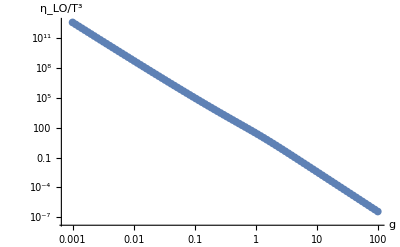

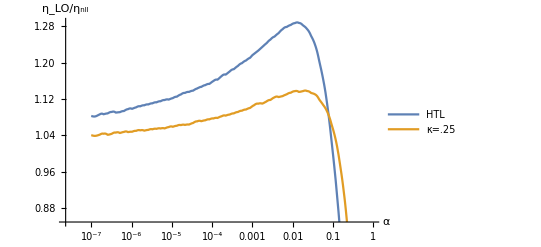

```mathematica
ηLO=Interpolation[$HTL,InterpolationOrder->5];
ηMeff=Interpolation[$Meff,InterpolationOrder->5];$HTL//ListLogLogPlot[#,AxesLabel->{"g","η_LO/T^3"}]&
Show[{
LogLinearPlot[{ηLO[√(4π α)]/ηNLL[α],ηMeff[√(4π α)]/ηNLL[α]},{α,10^-7,1},AxesLabel->{"α","η_LO/η_nll"},PlotLegends->{"HTL","κ=.25"}]
}]
```

#### eff model for w_tr

```mathematica
(* a = κ·4πα *)
Integrate[-t(1/(t-a))^2,{t,-s,0},Assumptions->{s>0,a>0}]
```

-s/(a+s)-Log[a/(a+s)]

```mathematica
(* weak coupling expansion *)
Series[%,{a,0,1}]
```

(-1-Log[a]-Log[1/s])+(2 a)/s+O[a]^2

```mathematica
(* here the log comes with prefac=1, which readily gives factor B for eff model *)
B=𝓈/0.3435548 /.𝓈->16 (4 π^2)/90
```

20.4287

```mathematica
c=Exp[2(1+Log[2]-EulerGamma+Zeta'[3]/Zeta[3])-1]//N
```

2.46506

```mathematica
κ=c/(4π)/0.608388
```

0.322432

```mathematica
i[a_,nmax_]:=NIntegrate[x/(E^x-1)(PolyLog[2,E^(-s/(4x))]-s/(4x)Log[1-E^(-s/(4x))])(Log[s/a+1]-s/(s+a)),{x,0,∞},{s,0,∞},Method->"AdaptiveMonteCarlo",AccuracyGoal->5,MaxPoints->nmax]/(4Zeta[3])^2
```

```mathematica
w[α_]:=B α^2 i[κ 4π α,10^5];
wl={((10^-#)^2)/(4π),w[((10^-#)^2)/(4π)]}&/@Range[-3,2,.2];
wTR=Interpolation[wl];
```

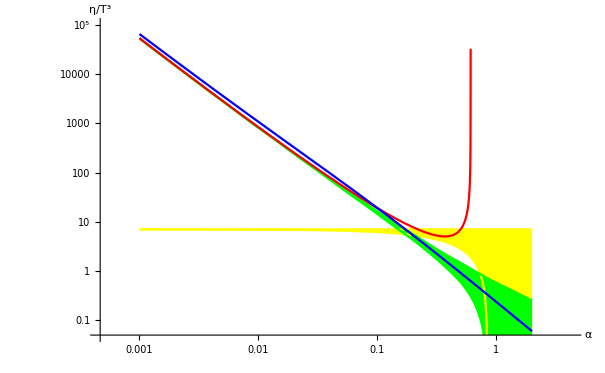

```mathematica
LogLogPlot[{
Max[16 (4 π^2)/90(1-15/(4π)α),0.001],16 (4 π^2)/90,
(16 (4 π^2)/90)/wTR[α],Max[(16 (4 π^2)/90(1-15/(4π)α))/wTR[α],0.001],
ηNLL[α] /. T->1, ηLO[√(4π α)]
},{α,10^-3,2},PlotRange->{0.05,10^5},PlotStyle->{Yellow,Yellow,Green,Green,Red,Blue,Cyan},Filling->{1->{{2},Yellow},3->{{4},Green}},AxesLabel->{α,"η/T^3"}]
```

```mathematica
Export["../data/eta_T3 [toy model.nb].dat",Array[{#,Max[16 (4 π^2)/90(1-15/(4π)#),10^-5],16. (4 π^2)/90,(16 (4 π^2)/90)/wTR[#],Max[(16 (4 π^2)/90(1-15/(4π)#))/wTR[#],10^-5], ηLO[√(4 π #)],ηNLL[#] /. {T->1}}&,32,{.001,0.8}]]
```

../data/eta_T3 [toy model.nb].dat

apparant discrepancy for α→0, factor  ~5%

## Part II: how to calc η(T)

```mathematica
σSB[nf_]:=(Gamma[4]Zeta[4])/(2 π^2)(2 8 + 7/8 2 2 nf 3 );
(* Nf, ϵ/T^4,s/T^4 *)
Array[{#,N[σSB[#]],4N[σSB[#]]/3}&,7,{0,6}]//TableForm
```

0 | 5.26379 | 7.01839
1 | 8.71815 | 11.6242
2 | 12.1725 | 16.23
3 | 15.6269 | 20.8358
4 | 19.0812 | 25.4416
5 | 22.5356 | 30.0475
6 | 25.99 | 34.6533

#### renormalised w_tr(T)

```mathematica
α[q2_]:=(4π/11)/Log[q2];
```

```mathematica
ℐren[temp_,nmax_]:=NIntegrate[x/(E^x-1)(PolyLog[2,E^(-s/(4  x))]-s/(4 x)Log[1-E^(-s/(4x))])(B Abs[t])/((t/α[Abs[t] temp^2] -κ(4π  ))^2),{x,0,∞},{s,0,∞},{t,-s,0},Method->"AdaptiveMonteCarlo",AccuracyGoal->5,MaxPoints->nmax]/(4Zeta[3])^2
```

```mathematica
ηosDATA={#,1/ℐren[#,10^5]}&/@Range[.5,10,.2];
ηos=(FitPolynomial[ηosDATA]/.{x-> #})&;
```

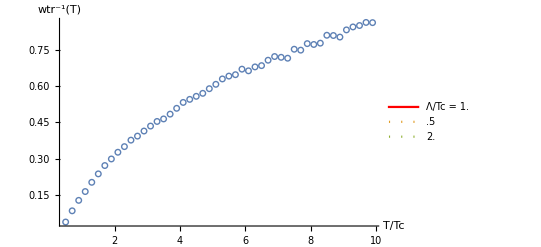

```mathematica
Show[{Plot[{ηos[T],ηos[T 2],ηos[T .5]},{T,1,10},AxesLabel->{"T/Tc","wtr^-1(T)"},PlotStyle->{Red,Dotted,Dotted},PlotRange->{0,1},PlotLegends->{"Λ/Tc = 1.",".5","2."}],ListPlot[ηosDATA,PlotMarkers->○]}]
```

#### Interacting entropy s(T)

```mathematica
(*
  Boyd [pure gauge]
http://arxiv.org/abs/hep-lat/9602007v1
*)
```

```mathematica
s0=Import["../data/Boyd1996_pes-spline.dat"][[3;;]]/.{a_,b_,c_,d_}->{a,d};
s0ι=Interpolation[s0,InterpolationOrder->2];
```

```mathematica
(*
  Borsanyi (note: units of Tc~150 MeV) [nf=3]
http://arxiv.org/abs/1309.5258
*)
```

```mathematica
s3=Import["../data/WB-EoS.dat"][[2;;]]/.{T_,i_,di_,p_,dp_,eps_,deps_,𝓈_,ds_,cs_,dcs_}-> {T/150,𝓈};
s3ι=Interpolation[s3,InterpolationOrder->2];
```

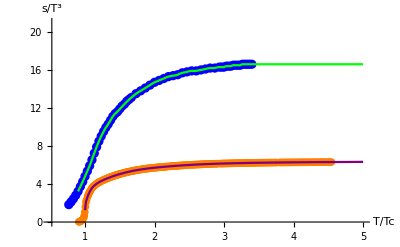

```mathematica
Show[{
ListPlot[s0,PlotStyle->Orange,PlotRange->{{.5,5},{0,21}},AxesLabel->{"T/Tc","s/T^3"}],
ListPlot[s3,PlotStyle->Blue],
Plot[s0ι[tt],{tt,1,5},PlotStyle->Purple,PlotRange->All],
Plot[s3ι[tt ],{tt ,0.9,5},PlotStyle->Green,PlotRange->All],
Plot[{4/3 σSB[0],4/3 σSB[3]},{tt ,4,5},PlotRange->All,PlotStyle->Gray]
}]
```

motivation to use more lattice data? (hotQCD, ...)

#### LO, renormalised η(T)

```mathematica
readEta[filename_]:=Cases[Import[filename],{_?NumberQ,___}];
FitPolynomial[data_]:=Fit[data,Table[x^n,{n,0,5}],x];
```

```mathematica
η0=readEta["../data/eta(T), HTL, Nf=0, l=1.csv"];
η3=readEta["../data/eta(T), HTL, Nf=3, l=1.csv"];
```

```mathematica
η0BAND=Transpose[η0/.{tt_,b_,b1_,b2_}->{{tt,b}, {tt,b1}, {tt,b2}}];
{η0M,η0L,η0U}=FitPolynomial/@η0BAND;
```

```mathematica
η3BAND=Transpose[η3/.{tt_,b_,b1_,b2_}->{{tt,b}, {tt,b1}, {tt,b2}}];
{η3M,η3L,η3U}=FitPolynomial/@η3BAND;
```

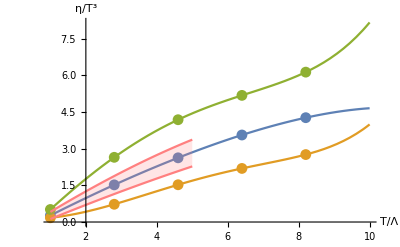

```mathematica
Show[{
Plot[{η0M,η0L,η0U},{x,1,10},AxesLabel->{"T/Λ","η/T^3"}],
ListPlot[η0BAND],
Plot[Evaluate[{η0M/.{x-> x .8},η0M/.{x-> 1.2x}}],{x,1,5},Filling->{1-> {2}},PlotStyle->Pink]
}]
```

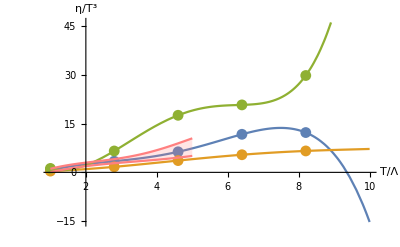

```mathematica
Show[{
Plot[{η3M,η3L,η3U},{x,1,10},AxesLabel->{"T/Λ","η/T^3"}],
ListPlot[η3BAND],
Plot[Evaluate[{η3M/.{x-> x .8},η3M/.{x-> 1.2x}}],{x,1,5},Filling->{1-> {2}},PlotStyle->Pink]
}]
```

#### finally: η(T)/s_lQCD

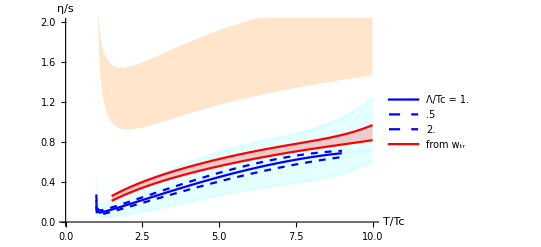

```mathematica
Show[{
Plot[{(η0M/.{x-> T})/s0ι[T],(η0L/.{x-> T})/s0ι[T],(η0U/.{x-> T})/s0ι[T]}
, {T,1,10},Filling->{2-> {3}},FillingStyle->Directive[Cyan,Opacity[.1]],PlotStyle->Directive[Cyan,Opacity[.1]],AxesLabel->{"T/Tc","η/s"},PlotRange->{0,2}],
Plot[{(η0M/.{x-> T})/s0ι[T],(η0M/.{x-> 1.1T})/s0ι[T],(η0M/.{x->.9 T})/s0ι[T]}
, {T,1,9},PlotStyle->{Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dashed]},PlotLegends->{"Λ/Tc = 1.",".5","2."}],
Plot[{ηos[.9T],ηos[1.1 T]},{T,1.5,10},PlotStyle->{Red},PlotLegends->{"from w_tr"},Filling->{1-> {2}}],
Plot[{ηNLL[ α[(π T)^2]]/s0ι[T],ηNLL[ α[(4π T)^2]]/s0ι[T]},{T,1,10},Filling-> {1-> {2}},PlotStyle->None,FillingStyle->Directive[Orange,Opacity[.2]]]
}]
```

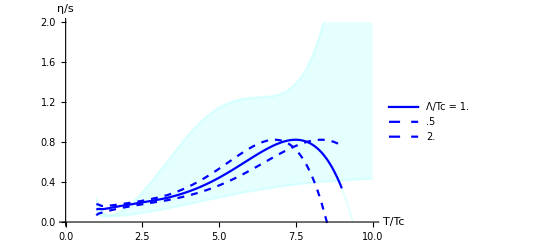

```mathematica
Show[{
Plot[{(η3M/.{x-> T})/s3ι[T],(η3L/.{x-> T})/s3ι[T],(η3U/.{x-> T})/s3ι[T]}
, {T,1,10},Filling->{2-> {3}},FillingStyle->Directive[Cyan,Opacity[.1]],PlotStyle->Directive[Cyan,Opacity[.1]],AxesLabel->{"T/Tc","η/s"},PlotRange->{0,2}],
Plot[{(η3M/.{x-> T})/s3ι[T],(η3M/.{x-> 1.1T})/s3ι[T],(η3M/.{x->.9 T})/s3ι[T]}
, {T,1,9},PlotStyle->{Directive[Blue,Thick],Directive[Blue,Dashed],Directive[Blue,Dashed]},PlotLegends->{"Λ/Tc = 1.",".5","2."}]
}]
```